_____________Ejercicio 1____________

31.998

28.0134

18.0153

4.0026

20.1797

39.948

83.798

8.31446

300

_____________ Funcion de distribución O_2(x) ___________

3.66599×10^-8 ⅇ^(-6.41413×10^-6 v^2) v^2

_____________ Funcion de distribución N_2(x) ___________

3.003×10^-8 ⅇ^(-5.6154×10^-6 v^2) v^2

_____________ Funcion de distribución H_2O(x) ___________

1.5487×10^-8 ⅇ^(-3.61123×10^-6 v^2) v^2

_____________ Funcion de distribución He(x) ___________

1.62189×10^-9 ⅇ^(-8.02338×10^-7 v^2) v^2

_____________ Funcion de distribución Ne(x) ___________

1.83603×10^-8 ⅇ^(-4.0451×10^-6 v^2) v^2

_____________ Funcion de distribución Ar(x) ___________

5.11387×10^-8 ⅇ^(-8.00774×10^-6 v^2) v^2

_____________ Funcion de distribución Kr(x) ___________

1.55367×10^-7 ⅇ^(-0.0000167976 v^2) v^2

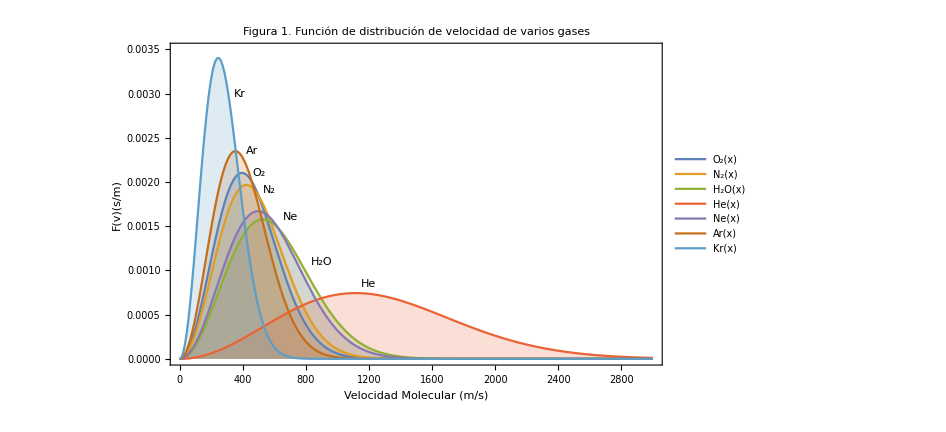

```mathematica
"_____________Ejercicio 1____________"

Clear[M1,M2,M3,M4,M5,M6,M7,R,T]
M1=31.998 (* g Subscript[O, 2] mol-1*)
M2=28.0134 (* g Subscript[N, 2] mol-1*)
M3=18.01528 (* g Subscript[H, 2] O mol-1*)
M4=4.002602 (* g He mol-1*)
M5=20.1797 (* g Ne mol-1*)
M6=39.948 (* g Ar mol-1*)
M7=83.798 (* g Kr mol-1*)
R=8.31446 (* J mol-1 K-1 *)
T=300 (* K *)

"_____________ Funcion de distribución O_2(x) ___________"
F1[v_]= 4π(M1/(2000π R T))^(3/2) v^2 ⅇ^((-M1 v^2)/(2000 R T))

"_____________ Funcion de distribución N_2(x) ___________"
F2[v_]= 4π(M2/(2000π R T))^(3/2) v^2 ⅇ^((-M2 v^2)/(2000 R T))

"_____________ Funcion de distribución H_2O(x) ___________"
F3[v_]= 4π(M3/(2000π R T))^(3/2) v^2 ⅇ^((-M3 v^2)/(2000 R T))

"_____________ Funcion de distribución He(x) ___________"
F4[v_]= 4π(M4/(2000π R T))^(3/2) v^2 ⅇ^((-M4 v^2)/(2000 R T))

"_____________ Funcion de distribución Ne(x) ___________"
F5[v_]= 4π(M5/(2000π R T))^(3/2) v^2 ⅇ^((-M5 v^2)/(2000 R T))

"_____________ Funcion de distribución Ar(x) ___________"
F6[v_]= 4π(M6/(2000π R T))^(3/2) v^2 ⅇ^((-M6 v^2)/(2000 R T))

"_____________ Funcion de distribución Kr(x) ___________"
F7[v_]= 4π(M7/(2000π R T))^(3/2) v^2 ⅇ^((-M7 v^2)/(2000 R T))

Show[Plot[{F1[v],F2[v],F3[v],F4[v],F5[v],F6[v],F7[v]},{v,0,3000},FrameLabel->{"Velocidad Molecular (m/s)",Row@{"F(v)(s/m)"}},PlotLabel->"Figura 1. Función de distribución de velocidad de varios gases",PlotLegends->{"O_2(x)","N_2(x)","H_2O(x)","He(x)","Ne(x)","Ar(x)","Kr(x)"},Filling->Axis,Frame->True,PlotRange->{{0,3000},{0,0.0035}},ImageSize->700,LabelStyle->{15,Black}],Graphics[Text["Kr",{380,0.0030}]],Graphics[Text["Ar",{460,0.00235}]],Graphics[Text["O_2",{500,0.0021}]],Graphics[Text["N_2",{565,0.00191}]],Graphics[Text["Ne",{700,0.0016}]],Graphics[Text["H_2O",{900,0.0011}]],Graphics[Text["He",{1200,0.00085}]]]
```

_____________Ejercicio 2_____________

16.0425

273

800

_____________ Función de distribución a T_1= 0.baC ___________

1.49918×10^-8 ⅇ^(-3.53383×10^-6 v^2) v^2

_____________ Función de distribución a T_2= 800 K ___________

2.98856×10^-9 ⅇ^(-1.20592×10^-6 v^2) v^2

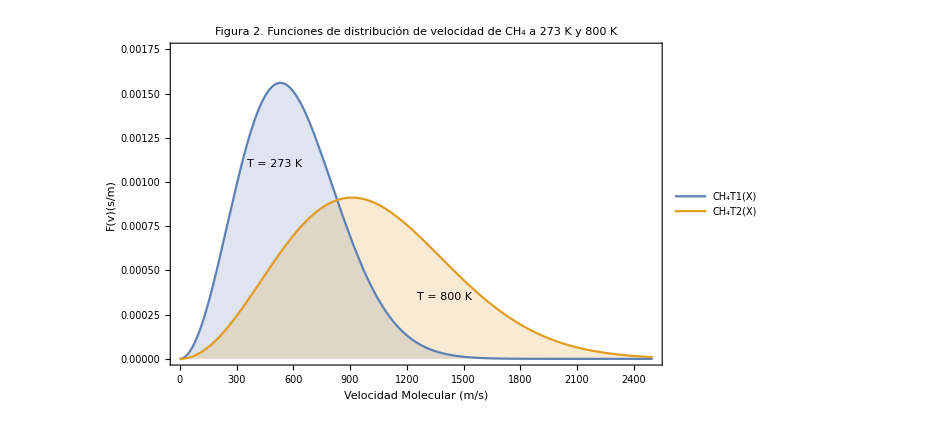

Al comparar ambos perfiles puede notarse que la función de distribución para una misma sustancia se distribuye entre un mayor rango de valores de la velocidad cuando aumenta la temperatura. De la misma manera, al asignar las rapideces más probable, media y raíz cuadrática media se podría observar que estas toman magnitudes mayores cuando la temperatura es mayor. Las anteriores descripciones se resumen en el hecho de que las distribuciones pueden ser más desplazadas hacia la derecha (más anchas) o no dependiendo del valor de la temperatura. Por otro lado, puede verse que la altura de los picos también es diferente, teniendo así la distribución de mayor temperatura un menor pico, lo cual puede verse directamente de la fórmula de la distribución, cuya amplitud es inversamente proporcional a T^(3/2).

```mathematica
"_____________Ejercicio 2_____________"

Clear[M8,T1,T2,k]
M8=16.0425 (* g Subscript[CH, 4] mol-1  *)
T1=273 (* K *)
T2=800 (* K *)

"_____________ Función de distribución a T_1= 0.baC ___________"
F8[v_]= 4π(M8/(2000π R T1))^(3/2) v^2 ⅇ^((-M8 v^2)/(2000 R T1))

"_____________ Función de distribución a T_2= 800 K ___________"
F9[v_]= 4π(M8/(2000π R T2))^(3/2) v^2 ⅇ^((-M8 v^2)/(2000 R T2))

Show[Plot[{F8[v],F9[v]},{v,0,2500},FrameLabel->{"Velocidad Molecular (m/s)",Row@{"F(v)(s/m)"}},PlotLabel->"Figura 2. Funciones de distribución de velocidad de CH_4 a 273 K y 800 K",PlotLegends->{"CH_4T1(X)","CH_4T2(X)"},Filling->Axis,Frame->True,PlotRange->{{0,2500},{0,0.00175}},ImageSize->700,LabelStyle->{15,Black}],Graphics[Text["T = 273 K",{500,0.0011}]],Graphics[Text["T = 800 K",{1400,0.00035}]]]
"Al comparar ambos perfiles puede notarse que la función de distribución para una misma sustancia se distribuye entre un mayor rango de valores de la velocidad cuando aumenta la temperatura. De la misma manera, al asignar las rapideces más probable, media y raíz cuadrática media se podría observar que estas toman magnitudes mayores cuando la temperatura es mayor. Las anteriores descripciones se resumen en el hecho de que las distribuciones pueden ser más desplazadas hacia la derecha (más anchas) o no dependiendo del valor de la temperatura. Por otro lado, puede verse que la altura de los picos también es diferente, teniendo así la distribución de mayor temperatura un menor pico, lo cual puede verse directamente de la fórmula de la distribución, cuya amplitud es inversamente proporcional a T^(3/2)."
```

```mathematica
"_____________Ejercicio 2a_____________"

Clear[M8,T1,NA,R,Pr]
M8=16.0425 (* g Subscript[CH, 4] mol-1  *)
T1=273 (* K *)
NA=6.022 10^23 (* moléculas *)
R=8.31446 (* J mol-1 K-1 *)

"El valor obtenido en la siguiente expresión corresponde a la probabilidad de que la velocidad de una molécula de CH_4 se encuentre entre 90.000 y 90.002 m/s."
Pr[v_]=∫_90.000^90.002 4π (M8/(2000π R T1))^(3/2) v^2 ⅇ^((-M8 v^2)/(2000 R T1))ⅆv 
"El número de moléculas cuya velocidad se encuentra en el intervalo mencionado anteriormente corresponde a:"

Subscript[N, v]=NA *Pr[v_] (* moléculas *)
```

_____________Ejercicio 2a_____________

16.0425

273

6.022×10^23

8.31446

El valor obtenido en la siguiente expresión corresponde a la probabilidad de que la velocidad de una molécula de CH_4 se encuentre entre 90.000 y 90.002 m/s.

2.36019×10^-7

El número de moléculas cuya velocidad se encuentra en el intervalo mencionado anteriormente corresponde a:

1.4213×10^17

```mathematica
"_____________Ejercicio 2b_____________"

"El valor obtenido en la siguiente expresión corresponde a la probabilidad de que la velocidad de una molécula de CH_4 se encuentre entre 415 y 800 m/s."
Pr[v_]=∫_415^800 4π (M8/(2000π R T1))^(3/2) v^2 ⅇ^((-M8 v^2)/(2000 R T1))ⅆv
"El número de moléculas cuya velocidad se encuentra en el intervalo mencionado anteriormente corresponde a:"

Subscript[N, v]=NA *Pr[v_] (* moléculas *)
```

_____________Ejercicio 2b_____________

El valor obtenido en la siguiente expresión corresponde a la probabilidad de que la velocidad de una molécula de CH_4 se encuentre entre 415 y 800 m/s.

0.538654

El número de moléculas cuya velocidad se encuentra en el intervalo mencionado anteriormente corresponde a:

3.24378×10^23

```mathematica
"_____________Ejercicio 2c_____________"

"Integrando la función (F(v)) a T = 273 K desde v = 0 hasta ∞ puede verificarse que está normalizada."
Pr[v_]=∫_0^∞ 4π (M8/(2000π R T1))^(3/2) v^2 ⅇ^((-M8 v^2)/(2000 R T1))ⅆv
```

_____________Ejercicio 2c_____________

Integrando la función (F(v)) a T = 273 K desde v = 0 hasta ∞ puede verificarse que está normalizada.

1.

_____________Ejercicio 2d_____________

Rapidez mas probable equivale a:

531.958

Su respectiva densidad de probabilidad corresponde a:

0.00156068

Rapidez media equivale a:

600.25

Su respectiva densidad de probabilidad corresponde a:

0.00151202

Rapidez raíz cuadrática media equivale a:

651.513

Su respectiva densidad de probabilidad corresponde a:

0.0014199

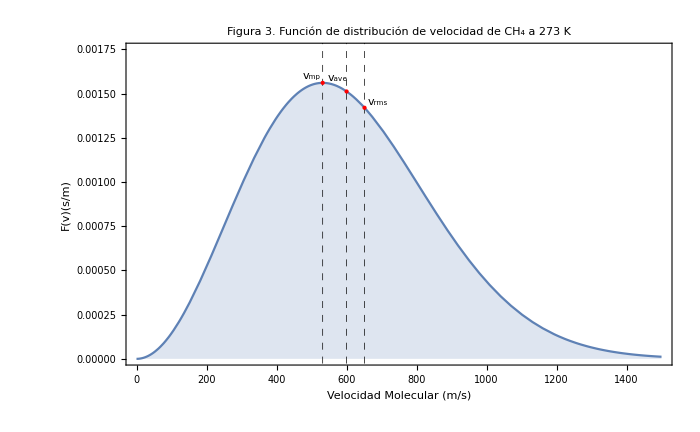

```mathematica
"_____________Ejercicio 2d_____________"

"Rapidez mas probable equivale a:"
v_mp=√((2000 R T1)/M8)  (* m/s *)
"Su respectiva densidad de probabilidad corresponde a:"
F8[√((2000 R T1)/M8)] (* s/m *)

"Rapidez media equivale a:"
v_ave=((8000 R T1)/(π M8))^(1/2) (* m/s *)
"Su respectiva densidad de probabilidad corresponde a:"
F8[((8000 R T1)/(π M8))^(1/2)](* s/m *)

"Rapidez raíz cuadrática media equivale a:"
v_rms=((3000 R T1)/M8)^(1/2) (* m/s *)
"Su respectiva densidad de probabilidad corresponde a:"
F8[((3000 R T1)/M8)^(1/2)] (* s/m *)

Show[Plot[F8[v],{v,0,1500},FrameLabel->{"Velocidad Molecular (m/s)",Row@{"F(v)(s/m)"}},PlotLabel->"Figura 3. Función de distribución de velocidad de CH_4 a 273 K",Filling->Axis,Frame->True,PlotRange->{{0,1500},{0,0.00175}},ImageSize->700,LabelStyle->{15,Black},GridLines->{{531.957971814941,600.2502931663619,651.5127977762211},None},GridLinesStyle->Directive[Black,Dashed]],Graphics[{PointSize[Large],Red,Point[{531.9579718149415,0.0015606777956699298}],Black,Text["v_mp",{500,0.0016}]}],Graphics[{PointSize[Large],Red,Point[{600.2502931663619,0.0015120179385987227}],Black,Text["v_ave",{575,0.00159}]}],Graphics[{PointSize[Large],Red,Point[{651.5127977762211,0.0014198983995098113}],Black,Text["v_rms",{690,0.00145}]}]]
```